Section 3: Statistical functions

```mathematica
Clear[ave,aveSqr,var,unc];
ave[myList_]:=Total[myList]/Length[myList]//N;
aveSqr[myList_]:=Total[myList^2]/Length[myList]//N;
var[myList_]:=aveSqr[myList]-ave[myList]^2;
unc[myList_]:=Sqrt[var[myList]/Length[myList]];
xcm [run_]:= ave[Transpose[run[[2]]]];
ycm[run_] := ave[Transpose[run[[2]]]];
r[run_]:= Sqrt[
var[Transpose[run][[1]]] + 
var[Transpose[run][[2]]]
]
```

```mathematica
DLA[s_Integer, n_Integer] :=
Module[{loc, rad, particleCount = 0,
stepChoices = {{1,0}, {0,1}, {-1, 0}, {0, -1}}},
occupiedSites = {{0,0}};
cellOverTime = {};
While[Length[occupiedSites] < n,
++particleCount;
rad = Max[Abs[occupiedSites]] + s;
loc = FixedPoint[
(# + stepChoices[[Random[Integer, {1,4}]]])&,
Round[rad {Cos[#], Sin[#]}]&[Random[Real,{0,N[2Pi]}]],
SameTest ->(Apply[Plus, #2^2] > (rad + s)^2 ||
Intersection[occupiedSites,
Map[Function[y, y + #2],
stepChoices]] != {} &)
];
If[Apply[Plus, loc^2] < rad^2,
occupiedSites = Join[occupiedSites, {loc}]];
AppendTo[cellOverTime,occupiedSites];
];
Print["The number of particles released was ", particleCount];
(*occupiedSites*)
cellOverTime
]
```

```mathematica
FractalDimension[occupiedSites_List]:=
Module[{occSiteDensity,fractalDataList,fractaldim},
occSiteDensity[t_Integer]:=
N[Count[occupiedSites,{x_?(Abs[#]<=t&),
y_?(Abs[#]<=t&)}]]/(2t+1)^2;
fractalDataList=Table[{2s,occSiteDensity[s]},
{s,Max[Abs[occupiedSites]]}];
fractaldim=Fit[N[Log[fractalDataList]],
{1,x},x];
Print["The fractal dimension of the DLA is    ",
Coefficient[fractaldim, x]];
]
```

```mathematica
FractalDimension[DLA[12,120]]
```

```mathematica
myCluster = DeleteDuplicates[DLA[10,1000]];
```

The number of particles released was 4069

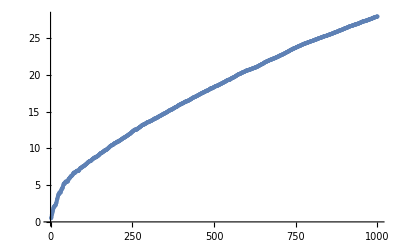

```mathematica
ListPlot[Table[{ Length[myCluster[[i]]], r[myCluster[[i]]]},{i,1,Length[myCluster]}]]
```